```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Antonio\Dropbox\4-ResearchProjects\01-Springer-Fractal Tumor Growth\nuevos datos\TNCI101

```mathematica
points =SemanticImport["3C-TB16-gliobastoma.txt"]
```

45.08 | -13.75 | -46.56
45.83 | -13.75 | -46.56
46.58 | -13.75 | -46.56
47.33 | -13.75 | -46.56
42.83 | -13. | -46.56
45.08 | -13. | -46.56
47.33 | -13. | -46.56
43.58 | -12.25 | -46.56
44.33 | -12.25 | -46.56
45.08 | -12.25 | -46.56
47.33 | -12.25 | -46.56
48.08 | -12.25 | -46.56
43.58 | -11.5 | -46.56
47.33 | -11.5 | -46.56
48.08 | -11.5 | -46.56
48.83 | -11.5 | -46.56
⋮_39515 |  | 
2 levels | 39531rows |  | Dataset[{__List}]

```mathematica
pointsf = Normal@points
```

{{45.0806,-13.7522,-46.562},{45.8306,-13.7522,-46.562},39527,{42.8306,30.4979,6.43797},{39.0806,28.2479,7.43797}}
 |  |  |  |

```mathematica
Clear[points]
```

## Volume of tumor’s interface

```mathematica
Show[Graphics3D[{PointSize[Small], Red,Point/@pointsf}]]
```

-Graphics3D-

```mathematica
centerOfMass = {Total [pointsf[[All, 1]]], Total [pointsf[[All, 2]]], Total [pointsf[[All, 3]]]}  / Length[pointsf]
```

{42.3318,8.98531,-21.0736}

```mathematica
tal =Reverse@SortBy[Tally[pointsf[[All, 3]]], Last]; tal // Short
```

{{-22.562,1358},{-26.562,1353},«52»,{7.43797,1}}

Z - coordinate with most points

```mathematica
p = First[tal][[1]]
```

-22.562

```mathematica
pointsInBiggestSlice =Select[pointsf,Last[#]==p&]; pointsInBiggestSlice // Short
```

{{41.3306,-28.0022,-22.562},«1356»,«1»}

```mathematica
pointsInBiggestSlice // Length
```

1358

## Visibility graph for biggest tumor slice (original ordering)

```mathematica
distancesFromCenterBiggestSlice = EuclideanDistance[centerOfMass, #]& /@ pointsInBiggestSlice;
```

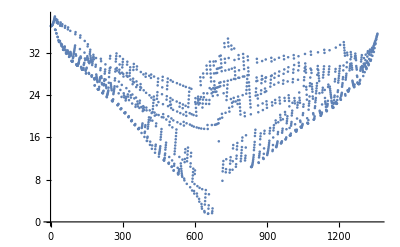
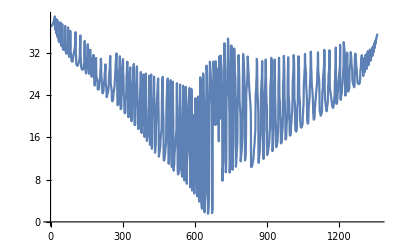

```mathematica
{ListPlot[distancesFromCenterBiggestSlice],ListLinePlot[distancesFromCenterBiggestSlice]}
```

```mathematica
fied[m_,n_,data_]:=If[(Min[#[[m]],#[[n]]]>Max[#[[m+1;;n-1]]])&@data,m<->n]
```

```mathematica
edgesDist=Cases[Flatten[Table[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&  @ distancesFromCenterBiggestSlice;
```

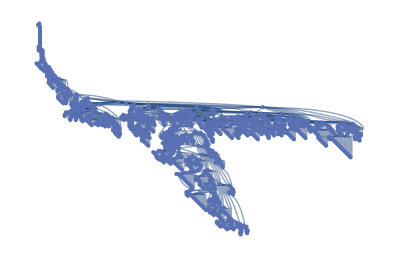

```mathematica
graphBiggestSlice =Graph[edgesDist,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Manipulate[Graph[edgesDist,GraphLayout->embedding], {embedding, {"LayeredDigraphEmbedding", "SpiralEmbedding", "RadialEmbedding","BalloonEmbedding","SpringEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding", "CircularEmbedding", "CircularMultipartiteEmbedding"}}]
```

Degree of vertices in biggest slice

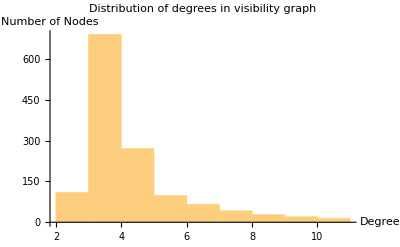

```mathematica
Histogram[VertexDegree[graphBiggestSlice],{Range[2,11]},PlotLabel->Style["Distribution of degrees in visibility graph","Subtitle",14],AxesLabel->{"Degree","Number of Nodes"}]
```

## All the tumor slices

```mathematica
distancesFromCenterAllTumor = EuclideanDistance[centerOfMass, #]& /@ pointsf
```

{34.2667,34.335,34.4195,34.5201,33.6653,33.7737,39520,34.9678,34.9382,34.9248,34.9274,34.5619}
 |  |  |  |

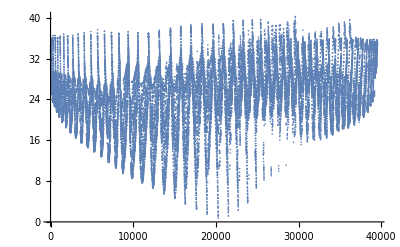

```mathematica
ListPlot[distancesFromCenterAllTumor]
```

```mathematica
distancesFromCenter = EuclideanDistance[centerOfMass, #]& /@ pointsf ;
```

## Visibility grah for the first 2000 points in the interface (original ordering)

```mathematica
dataS= distancesFromCenter[[1;;2000]];
```

```mathematica
edgesS=Cases[Flatten[Table[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&@dataS;
```

```mathematica
gS2000=Graph[#,GraphLayout->"LayeredDigraphEmbedding"]&@edgesS;
gSH2000=HighlightGraph[#,VertexList[#],VertexSize->Thread[VertexList[#]->Rescale[VertexDegree[#]]],ImageSize->{Automatic,500}]&@gS2000
```

-Graphics-

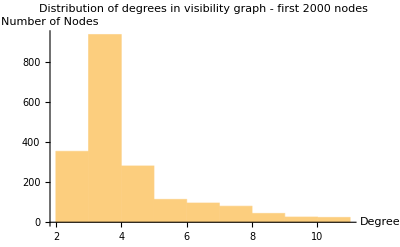

```mathematica
Histogram[VertexDegree[gS2000],{Range[2,11]},PlotLabel->Style["Distribution of degrees in visibility graph - first 2000 nodes","Subtitle",14],AxesLabel->{"Degree","Number of Nodes"}]
```

## Attempt of visibility graph for all distances (original ordering)

```mathematica
(*dataS={ distancesFromCenter};
edgesS=Cases[Flatten[ParallelTable[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&/@dataS;
$Aborted
gS=Graph[#,GraphLayout->"LayeredDigraphEmbedding"]&/@edgesS;*)
```

## Ordering of the points according to Travelling Salesman Problem solution

```mathematica
shortestTour =FindShortestTour[pointsf]
```

{43481.5,{1,6,5,8,10,9,13,18,26,20,17,25,27,21,28,22,29,71,80,81,198,366,365,361,362,194,357,618,916,621,625,39470,62,58,52,174,178,177,53,55,59,184,180,63,188,183,350,182,66,68,24,23,19,14,16,12,15,11,7,4,3,2,1}}
 |  |  |  |

Reorder points

```mathematica
tspPoints =pointsf[[Last[shortestTour]]]
```

{{45.0806,-13.7522,-46.562},{45.0806,-13.0021,-46.562},39528,{45.8306,-13.7522,-46.562},{45.0806,-13.7522,-46.562}}
 |  |  |  |

```mathematica
tspDistances =EuclideanDistance[centerOfMass, #]& /@ tspPoints
```

{34.2667,33.7737,33.6653,33.2001,33.2903,33.2368,39521,34.0308,34.5201,34.4195,34.335,34.2667}
 |  |  |  |

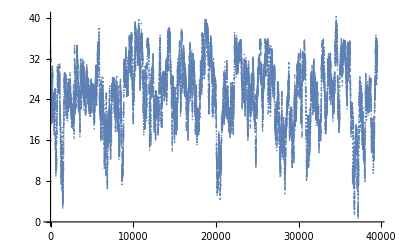

```mathematica
ListPlot[tspDistances]
```

## Visibility graph in slice with most tumor - Travelling Salesman Problem' s solution ordering

```mathematica
tspTourBigSlice =FindShortestTour[pointsInBiggestSlice]; tspTourBigSlice // Short
tspOrderPointsBigSlice =pointsInBiggestSlice[[Last[tspTourBigSlice]]]; tspOrderPointsBigSlice // Short
```

{1110.44,{1,21,20,19,25,24,30,«1345»,7,6,5,4,3,2,1}}

{{41.3306,-28.0022,-22.562},«1357»,«1»}

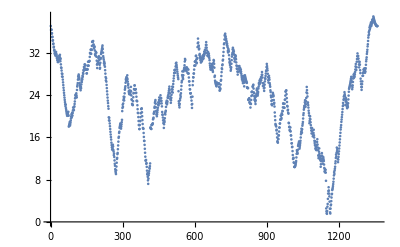
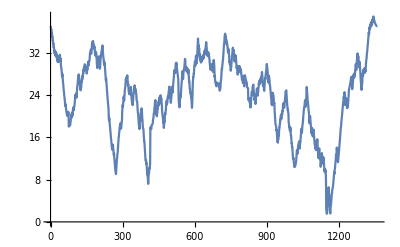

```mathematica
tspDistances = EuclideanDistance[centerOfMass, #]& /@ tspOrderPointsBigSlice; {ListPlot[tspDistances], ListLinePlot[tspDistances]}
```

### Estimation of the Hurst exponent of the “TSP walk”

```mathematica
pars=FindProcessParameters[tspDistances,FractionalBrownianMotionProcess[h]]
```

{h→0.901199}

Correlation plot

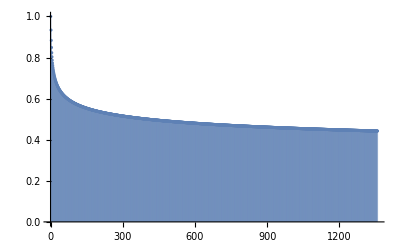

```mathematica
ListPlot[Table[CorrelationFunction[FractionalBrownianMotionProcess[h]/.pars,1,j],{j,Length[pointsInBiggestSlice]}],Filling->Axis,PlotRange->All]
```

```mathematica
edgesDistTSP=Cases[Flatten[Table[fied[m,n,#],{m,Length[#]},{n,m+1,Length[#]}]],_<->_]&  @ tspDistances; edgesDistTSP// Short
```

{1<->2,1<->3,1<->4,1<->1326,«2687»,1357<->1358,1357<->1359,1358<->1359}

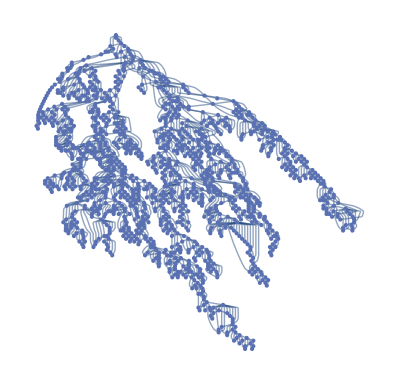

```mathematica
graphBiggestSliceTSP =Graph[edgesDistTSP,GraphLayout->"LayeredDigraphEmbedding"]
```

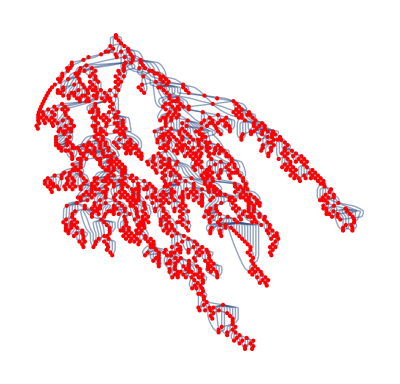

```mathematica
graphBiggestSliceTSPRed =Graph[edgesDistTSP,GraphLayout->"LayeredDigraphEmbedding", VertexStyle-> Red]
```

```mathematica
Manipulate[Graph[edgesDistTSP,GraphLayout->embedding], {embedding, {"SpringEmbedding", "SpiralEmbedding", "RadialEmbedding","BalloonEmbedding","SpringEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding", "CircularEmbedding", "CircularMultipartiteEmbedding"}}]
```

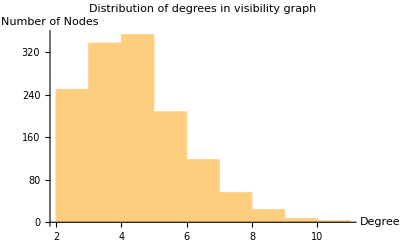

```mathematica
Histogram[VertexDegree[graphBiggestSliceTSP],{Range[2,11]},PlotLabel->Style["Distribution of degrees in visibility graph","Subtitle",14],AxesLabel->{"Degree","Number of Nodes"}]
```

## References

"Tumor Growth in the Brain: Complexity and Fractality", Martín-Landrove et al., to be published in Springer’s “The Fractal Geometry of the Brain”

“From Time Series to Complex Networks”, LaCasa et al.
http://www.pnas.org/content/105/13/4972.full

“Visibility graphs - dualism of time series and networks”, Vitaliy Kaurov
http://community.wolfram.com/groups/-/m/t/33771